```mathematica
Vec[n_]:=Table[Indexed[x,i],{i,n}]
```

```mathematica
Vec[52]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52}

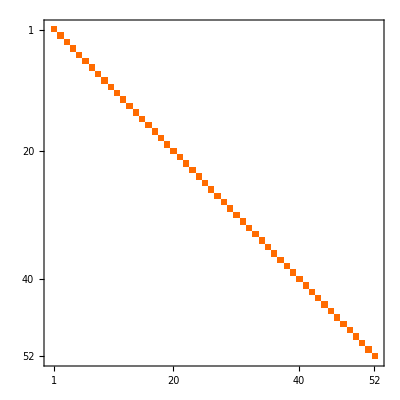
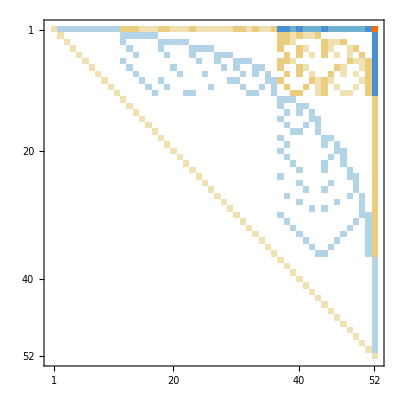
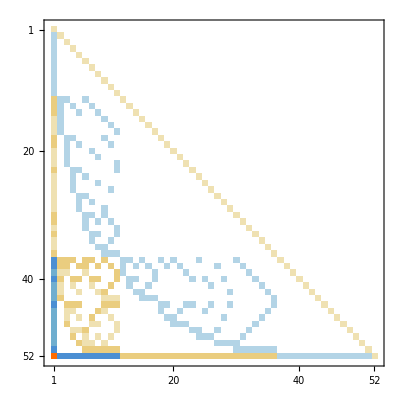
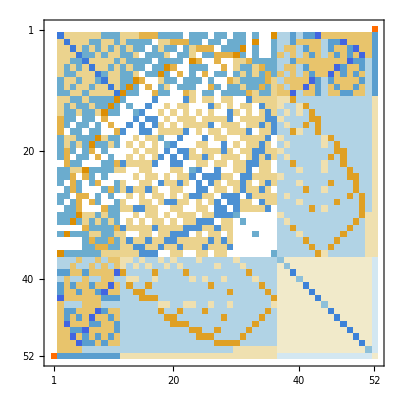
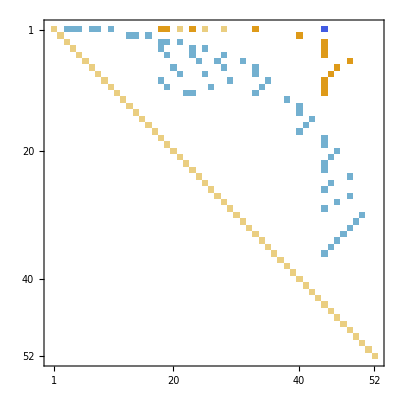
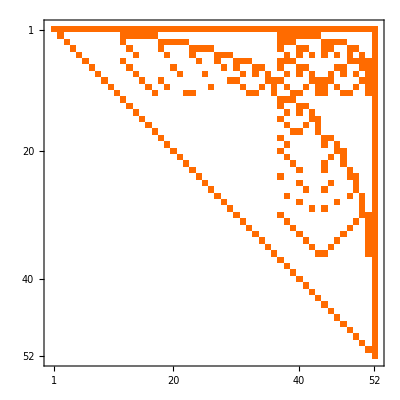
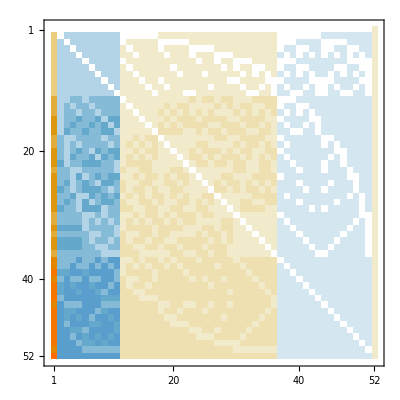
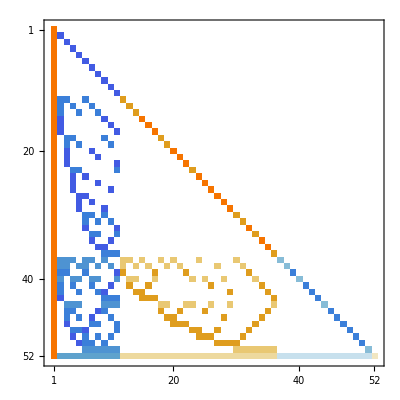
| C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2]],{base1,Keys[Bases]},{base2,Keys[Bases]}], TableHeadings->{Keys[Bases],Keys[Bases]}]
```

```mathematica
Vec[52].ConversionMatrix["E","C"]
```

{x1,x1+x2,x1+x3,x1+x4,x1+x5,x1+x6,x1+x7,x1+x8,x1+x9,x1+x10,x1+x11,x1+x2+x3+x6+x12,x1+x2+x4+x7+x13,x1+x2+x5+x8+x14,x1+x2+x9+x15,x1+x2+x10+x16,x1+x2+x11+x17,x1+x3+x4+x9+x18,x1+x3+x5+x10+x19,x1+x3+x7+x20,x1+x3+x8+x21,x1+x3+x11+x22,x1+x4+x5+x11+x23,x1+x4+x6+x24,x1+x4+x8+x25,x1+x4+x10+x26,x1+x5+x6+x27,x1+x5+x7+x28,x1+x5+x9+x29,x1+x6+x7+x9+x30,x1+x6+x8+x10+x31,x1+x6+x11+x32,x1+x7+x8+x11+x33,x1+x7+x10+x34,x1+x8+x9+x35,x1+x9+x10+x11+x36,x1+x2+x3+x4+x6+x7+x9+x12+x13+x15+x18+x20+x24+x30+x37,x1+x2+x3+x5+x6+x8+x10+x12+x14+x16+x19+x21+x27+x31+x38,x1+x2+x3+x6+x11+x12+x17+x22+x32+x39,x1+x2+x4+x5+x7+x8+x11+x13+x14+x17+x23+x25+x28+x33+x40,x1+x2+x4+x7+x10+x13+x16+x26+x34+x41,x1+x2+x5+x8+x9+x14+x15+x29+x35+x42,x1+x2+x9+x10+x11+x15+x16+x17+x36+x43,x1+x3+x4+x5+x9+x10+x11+x18+x19+x22+x23+x26+x29+x36+x44,x1+x3+x4+x8+x9+x18+x21+x25+x35+x45,x1+x3+x5+x7+x10+x19+x20+x28+x34+x46,x1+x3+x7+x8+x11+x20+x21+x22+x33+x47,x1+x4+x5+x6+x11+x23+x24+x27+x32+x48,x1+x4+x6+x8+x10+x24+x25+x26+x31+x49,x1+x5+x6+x7+x9+x27+x28+x29+x30+x50,x1+x6+x7+x8+x9+x10+x11+x30+x31+x32+x33+x34+x35+x36+x51,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20+x21+x22+x23+x24+x25+x26+x27+x28+x29+x30+x31+x32+x33+x34+x35+x36+x37+x38+x39+x40+x41+x42+x43+x44+x45+x46+x47+x48+x49+x50+x51+x52}

```mathematica
Vec[52].ConversionMatrix["G","C"]
```

{x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20+x21+x22+x23+x24+x25+x26+x27+x28+x29+x30+x31+x32+x33+x34+x35+x36+x37+x38+x39+x40+x41+x42+x43+x44+x45+x46+x47+x48+x49+x50+x51+x52,x2+x12+x13+x14+x15+x16+x17+x37+x38+x39+x40+x41+x42+x43+x52,x3+x12+x18+x19+x20+x21+x22+x37+x38+x39+x44+x45+x46+x47+x52,x4+x13+x18+x23+x24+x25+x26+x37+x40+x41+x44+x45+x48+x49+x52,x5+x14+x19+x23+x27+x28+x29+x38+x40+x42+x44+x46+x48+x50+x52,x6+x12+x24+x27+x30+x31+x32+x37+x38+x39+x48+x49+x50+x51+x52,x7+x13+x20+x28+x30+x33+x34+x37+x40+x41+x46+x47+x50+x51+x52,x8+x14+x21+x25+x31+x33+x35+x38+x40+x42+x45+x47+x49+x51+x52,x9+x15+x18+x29+x30+x35+x36+x37+x42+x43+x44+x45+x50+x51+x52,x10+x16+x19+x26+x31+x34+x36+x38+x41+x43+x44+x46+x49+x51+x52,x11+x17+x22+x23+x32+x33+x36+x39+x40+x43+x44+x47+x48+x51+x52,x12+x37+x38+x39+x52,x13+x37+x40+x41+x52,x14+x38+x40+x42+x52,x15+x37+x42+x43+x52,x16+x38+x41+x43+x52,x17+x39+x40+x43+x52,x18+x37+x44+x45+x52,x19+x38+x44+x46+x52,x20+x37+x46+x47+x52,x21+x38+x45+x47+x52,x22+x39+x44+x47+x52,x23+x40+x44+x48+x52,x24+x37+x48+x49+x52,x25+x40+x45+x49+x52,x26+x41+x44+x49+x52,x27+x38+x48+x50+x52,x28+x40+x46+x50+x52,x29+x42+x44+x50+x52,x30+x37+x50+x51+x52,x31+x38+x49+x51+x52,x32+x39+x48+x51+x52,x33+x40+x47+x51+x52,x34+x41+x46+x51+x52,x35+x42+x45+x51+x52,x36+x43+x44+x51+x52,x37+x52,x38+x52,x39+x52,x40+x52,x41+x52,x42+x52,x43+x52,x44+x52,x45+x52,x46+x52,x47+x52,x48+x52,x49+x52,x50+x52,x51+x52,x52}

```mathematica
Vec[52]/.With[{vec1=Vec[52].ConversionMatrix["E","C"],vec2=Vec[52].ConversionMatrix["C","G"]},
Solve[Fold[And,Table[vec1[[k]]==vec2[[k]],{k,Length[vec1]}]]]]//Sort//Flatten
```

{0,0,0,0,0,0,0,0,0,0,0,x12,x13,x14,x15,x16,-x12-x13-x14-x15-x16,x18,x19,x20,x21,-x12-x18-x19-x20-x21,-x12-x13-x14-x18-x19,-x15-x20,x25,x12+x14+x15+x19+x20-x25,-x16-x21,x12+x13+x14+x15+x16-x25,-x14-x15+x18+x21+x25,-x12-x13-x18,-x12-x14-x19,x12+x13+x14+x15+x16+x18+x19+x20+x21,x12+x18+x19,-x12-x13-x14-x15-x16-x19-x20+x25,-x18-x21-x25,x12+x13+x14,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[ShowGraph5Least[k],{k,allGraphs5GeneratorAtomKeys}]
```

{-Graphics-034,-Graphics-291608,-Graphics-295111,-Graphics-295230,-Graphics-295240,-Graphics-295210,-Graphics-295150,-Graphics-294970,-Graphics-294881,-Graphics-294430,-Graphics-294400,-Graphics-294151,-Graphics-292801,-Graphics-292810,-Graphics-292511,-Graphics-291911,-Graphics-287950,-Graphics-287861,-Graphics-287141,-Graphics-285521,-Graphics-284625,-Graphics-273370,-Graphics-273340,-Graphics-273100,-Graphics-270941,-Graphics-270643,-Graphics-266071,-Graphics-263645,-Graphics-229621,-Graphics-229630,-Graphics-229360,-Graphics-228820,-Graphics-228543,-Graphics-222311,-Graphics-221503,-Graphics-207671,-Graphics-207403,-Graphics-200348,-Graphics-98285,-Graphics-98401,-Graphics-98410,-Graphics-98381,-Graphics-98321,-Graphics-90851,-Graphics-90765,-Graphics-75731,-Graphics-75703,-Graphics-68168,-Graphics-30365,-Graphics-30371,-Graphics-22788,-Graphics-7608}

```mathematica
ShowGrap3[k_]:=Tooltip[ShowGraph[allGraphs3,k],allGraphs3[k,"compwhy"]]
```

```mathematica
Table[ShowGrap3[k],{k,allGraphs3GeneratorAtomKeys}]
```

{-Graphics-0,-Graphics-4,-Graphics-10,-Graphics-12,-Graphics-13}

```mathematica
ShowGrap2[k_]:=Tooltip[ShowGraph[allGraphs2,k],allGraphs2[k,"compwhy"]]
```

```mathematica
Table[ShowGrap2[k],{k,allGraphs2GeneratorAtomKeys}]
```

{-Graphics-0,-Graphics-1}

```mathematica
Table[ShowGrap2[k],{k,Keys[allGraphs2]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2}

```mathematica
Table[ShowGrap3[k],{k,Keys[allGraphs3]}]
```

{-Graphics-0,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-10,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-1,-Graphics-2}

```mathematica
Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==2&]
```

{14,16,18,22,6,2}

```mathematica
Table[ShowGrap3[k],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==2&]}]
```

{-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-6,-Graphics-2}

```mathematica
Keys[allGraphs2[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
Bases3=DefineOrLoad["Bases3",
Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs3],Length[ListofVars[allGraphs3[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs3[#1,result[base,"Colofour"]],allGraphs3[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs3[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]&
];
```

Saved C:\saved\symbols\Bases3.m

```mathematica
RepGraph3[base_]:=Table[allGraphs3[key,Bases3[base,"Colofour"]]->ShowGrap3[key],{key,Bases3[base,"AtomKeys"]}]
```

```mathematica
RepGraph3["E"]
```

{n1x2x3→-Graphics-0,n12x3→-Graphics-18,n13x2→-Graphics-6,n1x23→-Graphics-2,n123→-Graphics-26}

```mathematica
Table[ShowGrap3[k]->(allGraphs3[k,"colofourrealnull"]/.RepGraph3["E"]),{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==2&]}]
```

{-Graphics-14→--Graphics-26+-Graphics-2,-Graphics-16→--Graphics-26+-Graphics-6,-Graphics-18→-Graphics-18,-Graphics-22→--Graphics-26+-Graphics-18,-Graphics-6→-Graphics-6,-Graphics-2→-Graphics-2}

```mathematica
BaseCoeff3[key_,base_]:=Table[Coefficient[allGraphs3[key,Bases3[base,"Colofour"]],var],{var,Bases3[base,"Variables"]}]
```

```mathematica
BaseCoeff3[0,"E"]
```

{1,0,0,0,0}

```mathematica
Table[ShowGrap3[k]->(allGraphs3[k,"colofourrealnull"]/.RepGraph3["E"]),{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]
```

{-Graphics-0→-Graphics-0,-Graphics-9→--Graphics-18+-Graphics-0,-Graphics-12→-Graphics-26--Graphics-18--Graphics-6+-Graphics-0,-Graphics-13→2 -Graphics-26--Graphics-18--Graphics-6--Graphics-2+-Graphics-0,-Graphics-10→-Graphics-26--Graphics-18--Graphics-2+-Graphics-0,-Graphics-3→--Graphics-6+-Graphics-0,-Graphics-4→-Graphics-26--Graphics-6--Graphics-2+-Graphics-0,-Graphics-1→--Graphics-2+-Graphics-0}

```mathematica
Table[BaseCoeff3[k,"E"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==2&]}]//MatrixRank
```

4

```mathematica
Table[BaseCoeff3[k,"E"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]//MatrixRank
```

5

```mathematica
Table[BaseCoeff[k,"E"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==4&]}]//MatrixRank
```

51

```mathematica
Table[BaseCoeff6[k,"E"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==5&]}]//MatrixRank
```

202

```mathematica
Table[BaseCoeff6[k,"E"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==4&]}]//MatrixRank
```

187

```mathematica
Table[BaseCoeff6[k,"E"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==3&]}]//MatrixRank
```

122

```mathematica
Table[Table[BaseCoeff6[k,"E"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==max&]}]//MatrixRank,{max,6}]
```

{1,32,122,187,202,203}

```mathematica
Table[Table[BaseCoeff6[k,"G"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==max&]}]//MatrixRank,{max,6}]
```

{1,32,122,187,202,203}